```mathematica
experiments={
"EYrainbow_glucose",
"EYrainbow_glucose_largerBF",
"EYrainbow_rapamycin_1stTry",
"EYrainbow_rapamycin_CheckBistability",
"EYrainbow_1nmpp1_1st",
"EYrainbow_leucine_large",
"EYrainbowWhi5Up_betaEstrodiol"
};
data = Import[FileNameJoin[{NotebookDirectory[],"fitCellSizeWithOrganelle.csv"}],"Data","HeaderLines"->1];
epsilon = 10^(-18);
filled = data/.{0.->epsilon};
washed = Select[data,Function[x,NoneTrue[x,#==0&]]];
```

```mathematica
washed[[All,{2,-1}]]
```

```mathematica
Min[washed[[All,2]]]
```

0.03362

```mathematica
organelles = {"peroxisome","vacuole","ER","golgi","mito","LD"};
```

Vol_cell vs size_peroxisome:

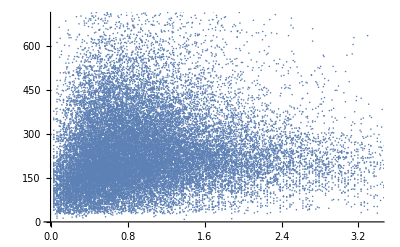

Vol_cell vs size_vacuole:

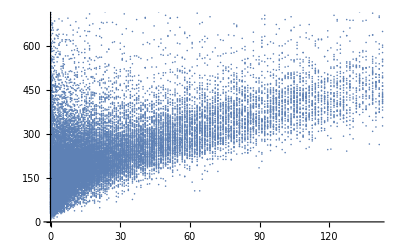

Vol_cell vs size_ER:

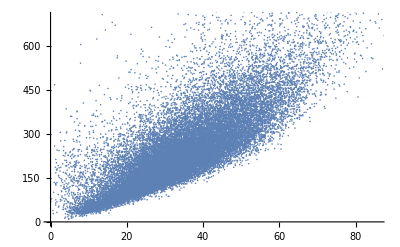

Vol_cell vs size_golgi:

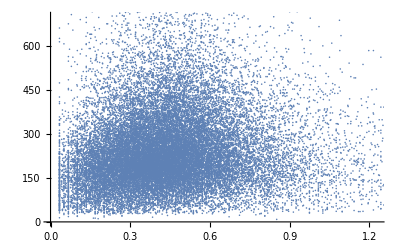

Vol_cell vs size_mito:

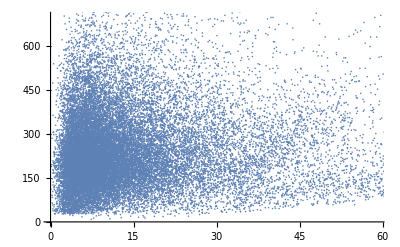

Vol_cell vs mito_LD:

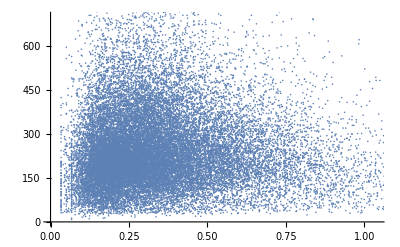

Vol_cell vs n_peroxisome:

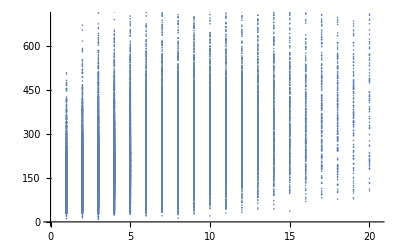

Vol_cell vs n_vacuole:

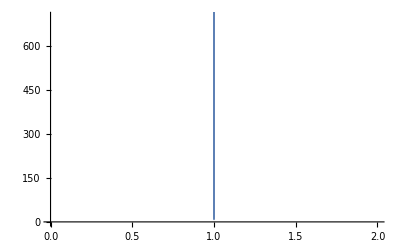

Vol_cell vs n_ER:

-Graphics-

Vol_cell vs n_golgi:

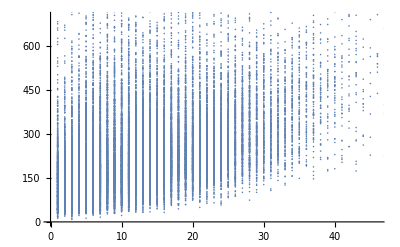

Vol_cell vs n_mito:

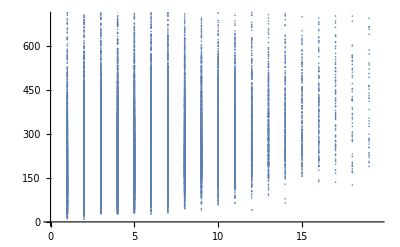

Vol_cell vs n_LD:

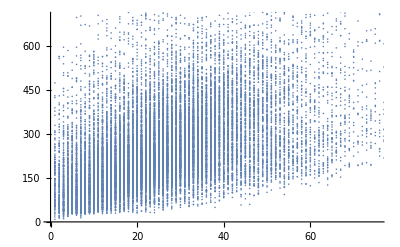

```mathematica
properties = {"experiment","size_peroxisome","size_vacuole","size_ER","size_golgi","size_mito","size_LD","n_peroxisome","n_vacuole","n_ER","n_golgi","n_mito","n_LD"};
Do[
Print["Vol_cell vs ",properties[[i]],": "];
Print[FindFormula[washed[[All,{i,-1}]],x,5,All]];
Print[ListPlot[washed[[All,{i,-1}]]]],
{i,2,13}
]
```

```mathematica
totalWashed = Transpose[Map[Times[Transpose[washed][[#]],Transpose[washed][[#+6]]]&,Table[i,{i,2,7}]]];
```

```mathematica
totalWashed = Transpose[Append[Transpose[totalWashed],washed[[All,-1]]]];
```

Vol_cell vs totalVolume_peroxisome:

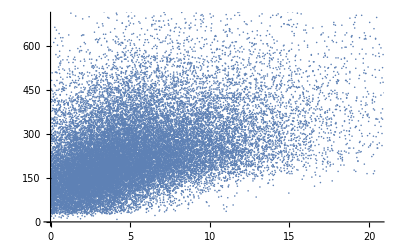

Vol_cell vs totalVolume_vacuole:

-Graphics-

Vol_cell vs totalVolume_ER:

-Graphics-

Vol_cell vs totalVolume_golgi:

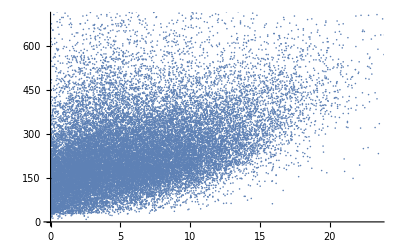

Vol_cell vs totalVolume_mito:

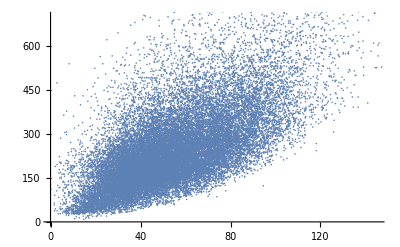

Vol_cell vs totalVolume_LD:

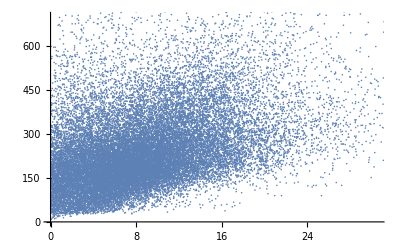

```mathematica
Do[
Print["Vol_cell vs totalVolume_",organelles[[i]],": "];
Print[FindFormula[totalWashed[[All,{i,-1}]],x,5,All]];
Print[ListPlot[totalWashed[[All,{i,-1}]]]],
{i,1,6}
]
```

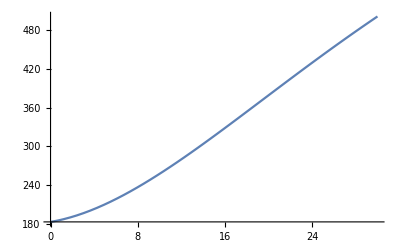

```mathematica
Plot[182.6350214726042+2.7968528622706206 x+0.6040857235326236 x^2-0.015100207756120356 x^3+0.00012185888625545253 x^4,{x,0,30}]
```

Vol_cell vs CrossTerm: peroxisome, peroxisome

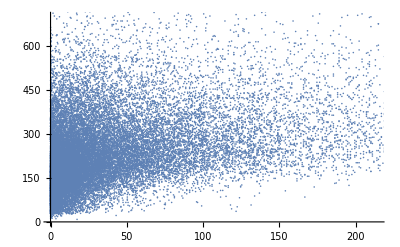

Vol_cell vs CrossTerm: peroxisome, vacuole

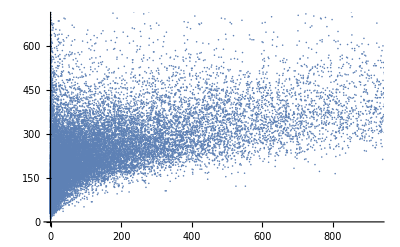

Vol_cell vs CrossTerm: peroxisome, ER

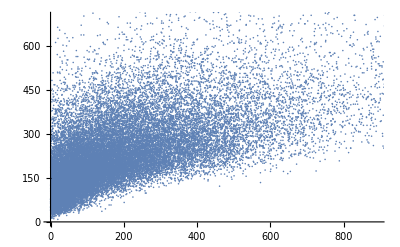

Vol_cell vs CrossTerm: peroxisome, golgi

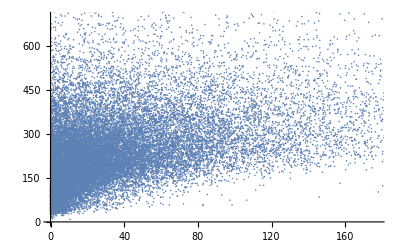

Vol_cell vs CrossTerm: peroxisome, mito

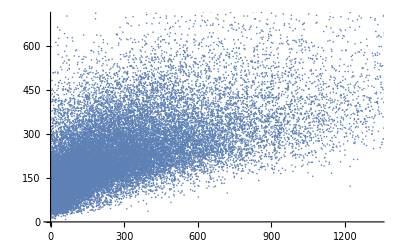

Vol_cell vs CrossTerm: peroxisome, LD

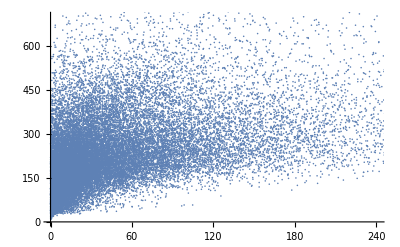

Vol_cell vs CrossTerm: vacuole, vacuole

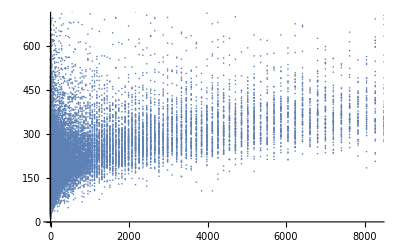

Vol_cell vs CrossTerm: vacuole, ER

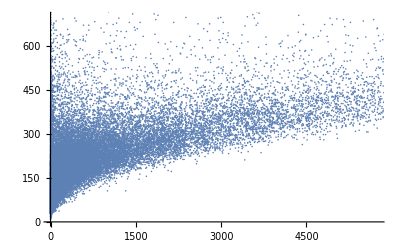

Vol_cell vs CrossTerm: vacuole, golgi

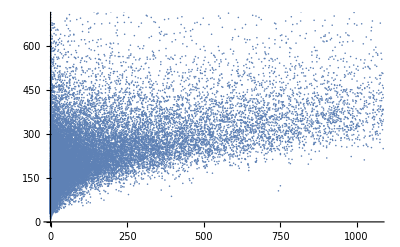

Vol_cell vs CrossTerm: vacuole, mito

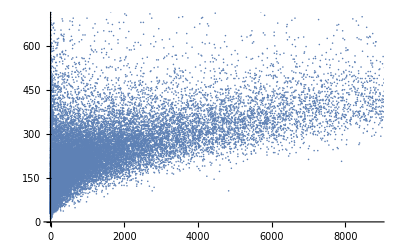

Vol_cell vs CrossTerm: vacuole, LD

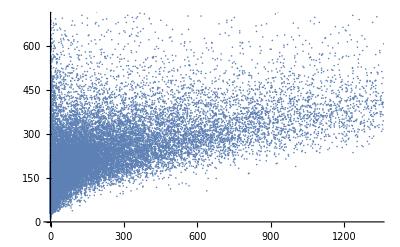

Vol_cell vs CrossTerm: ER, ER

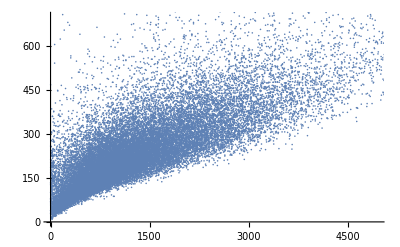

Vol_cell vs CrossTerm: ER, golgi

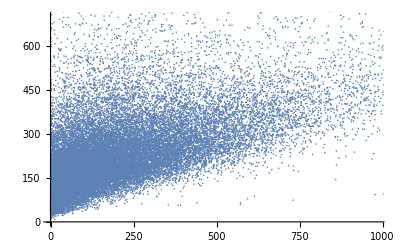

Vol_cell vs CrossTerm: ER, mito

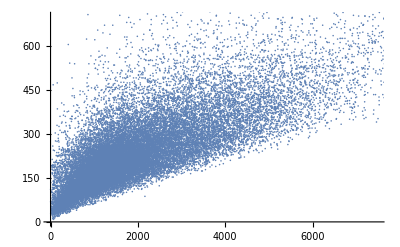

Vol_cell vs CrossTerm: ER, LD

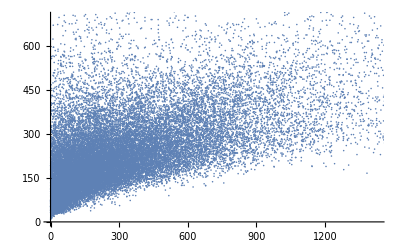

Vol_cell vs CrossTerm: golgi, golgi

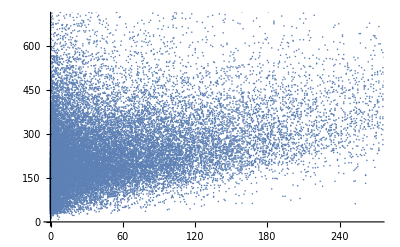

Vol_cell vs CrossTerm: golgi, mito

-Graphics-

Vol_cell vs CrossTerm: golgi, LD

-Graphics-

Vol_cell vs CrossTerm: mito, mito

-Graphics-

Vol_cell vs CrossTerm: mito, LD

-Graphics-

Vol_cell vs CrossTerm: LD, LD

-Graphics-

```mathematica
Do[
Print["Vol_cell vs CrossTerm: ",organelles[[i]],", ",organelles[[j]]];
toFit = Transpose[{Times[totalWashed[[All,i]],totalWashed[[All,j]]],totalWashed[[All,-1]]}];
Print[FindFormula[toFit,x,5,All]];
Print[ListPlot[toFit]],
{i,1,6},{j,i,6}
]
```

```mathematica
{Table[i,{i,1,3}],Table[j,{j,1,3}]}
```

{{1,2,3},{1,2,3}}

```mathematica
totalWashed
```